```mathematica
NSolve[x+Sqrt[x^2+2000]+Sqrt[x^2+2070]==230,x]
```

{{x→-220.881},{x→67.5479}}

```mathematica
67.55^2
```

4563.

```mathematica
{x,Sqrt[x^2+2000],Sqrt[x^2+2070]}/.x->0.
Total[%]
```

{0.,44.7214,45.4973}

90.2186

```mathematica
Total[%]
```

```mathematica
72.1^2
```

5198.41

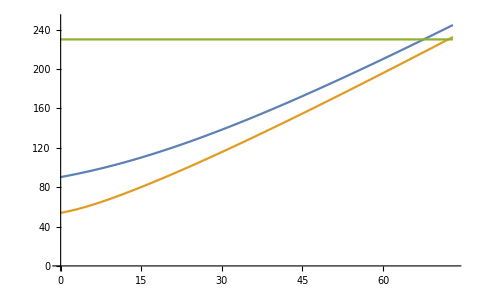

```mathematica
Plot[{x+Sqrt[x^2+2000]+Sqrt[x^2+2070],x+Sqrt[x^2+70]+Sqrt[x^2+2070],230},{x,0,73},PlotRange->{0,250}]
```

```mathematica
ind[p_]:=If[p,1,None]
```

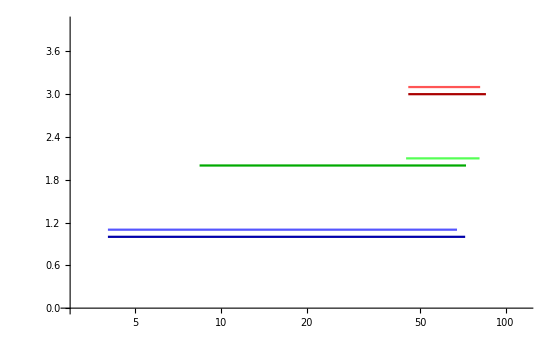

```mathematica
LogLinearPlot[{ind[0<x<72.1],1.1ind[0<x<67.5],2ind[8.4<x<72.6],2.1ind[44.7<x<81],3ind[45.5<x<85.3],3.1ind[45.5<x<81.4]},{x,4,100},PlotRange->{0,4},PlotStyle->{Darker@Blue,Lighter[Blue],Darker@Green,Lighter[Green],Darker@Red,Lighter[Red]}]
```

```mathematica
massesNH[x_]:={x,Sqrt[x^2+70],Sqrt[x^2+2070]}
massesIH[x_]:={x,Sqrt[x^2+2000],Sqrt[x^2+2070]}
```

```mathematica
Join[massesNH[x],massesIH[x]]
```

{x,√(70+x^2),√(2070+x^2),x,√(2000+x^2),√(2070+x^2)}

```mathematica
ind[p_]:=If[p,10^3,10^-3]
```

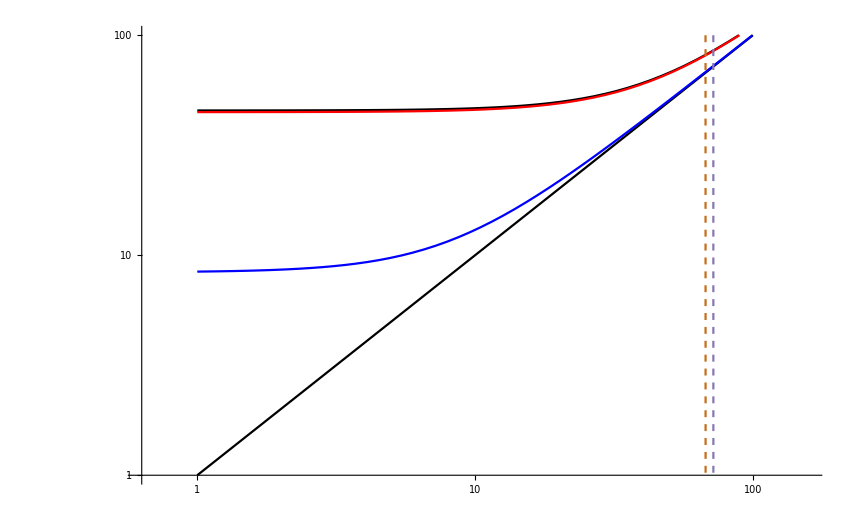

```mathematica
LogLogPlot[{x,√(70+x^2),√(2070+x^2),√(2000+x^2),ind[x+√(70+x^2)+√(2070+x^2)<230],ind[x+√(2000+x^2)+√(2070+x^2)<230]},{x,1,100},PlotRange->{1,100},PlotStyle->{Black,Blue,Black,Red,Dashed,Dashed}]
```

```mathematica
Solve[Sqrt[x^2+70]/x==Sqrt[x^2+2070]/Sqrt[x^2+70],x]//N
```

{{x→1.59338}}

```mathematica
massesNH[1.593]
```

{1.593,8.5169,45.5251}

```mathematica
85.3/67.5
85.3/45.5
```

1.2637

1.87473